## Figure 5

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Data-Work\works\ArtemisininResistance\Stan\Recovery

```mathematica
PLchn=Import["PL-stan-output.csv"];
WPchn=Import["WP-stan-output.csv"];
```

## The population mean parameters

```mathematica
ListParPos=38;
ChainBeg=43;
ChainEnd=1042;
```

```mathematica
PLchn[[ListParPos,8;;20]]
```

{N0_mean,mu_mean,sig_mean,pmr_mean,gamma_mean,ec50_mean,deadrateR_mean,deadrateT_mean,deadrateS_mean,recoverrateR_mean,recoverrateT_mean,recoverrateS_mean,recoverlag_mean}

```mathematica
ParPosIndx=Thread[PLchn[[ListParPos,8;;20]]->Range[8,20]]
```

{N0_mean→8,mu_mean→9,sig_mean→10,pmr_mean→11,gamma_mean→12,ec50_mean→13,deadrateR_mean→14,deadrateT_mean→15,deadrateS_mean→16,recoverrateR_mean→17,recoverrateT_mean→18,recoverrateS_mean→19,recoverlag_mean→20}

```mathematica
pars={"N_0","μ","σ","PMF","γ","EC_50","Dead_R","Dead_T","Dead_S","Recovery_R","Recovery_T","Recovery_S","lag"}
```

{N_0,μ,σ,PMF,γ,EC_50,Dead_R,Dead_T,Dead_S,Recovery_R,Recovery_T,Recovery_S,lag}

```mathematica
ylabels={"log_10number of initial parasites (N_0)","Mean age of parasites (hrs)","SD of the age of parasites (hrs)","Parasite multiplication factor (/48 hrs)","The slope constant","EC_50 of the damaged effect (ng/ml)","Dead rate of Rings", "Dead rate of Trophozoites","Dead rate of Schizonts","Recovery rate of Rings","Recovery rate of Trophozoites","Recovery rate of Schizonts","Recovery lag time (hrs)"}
```

{log_10number of initial parasites (N_0),Mean age of parasites (hrs),SD of the age of parasites (hrs),Parasite multiplication factor (/48 hrs),The slope constant,EC_50 of the damaged effect (ng/ml),Dead rate of Rings,Dead rate of Trophozoites,Dead rate of Schizonts,Recovery rate of Rings,Recovery rate of Trophozoites,Recovery rate of Schizonts,Recovery lag time (hrs)}

```mathematica
ParPosition[par_,site_]:=Position[If[StringMatchQ["PL",site],PLchn[[ListParPos]],WPchn[[ListParPos]]],s_String/;StringMatchQ[s,par]][[1,1]]
```

```mathematica
PLchnDat=PLchn[[ChainBeg;;ChainEnd,All]];
WPchnDat=WPchn[[ChainBeg;;ChainEnd,All]];
```

### Pailin

```mathematica
ACTpars="AS7CT."<>ToString@#&/@Range[1,20];
SplitACTpars="SplitCT."<>ToString@#&/@Range[1,20];
```

```mathematica
PLid={"P002","P003","P006","P008","P009","P011","P013","P014","P018","P020","P021","P022","P023","P025","P030","P031","P033","P035","P037","P039"};
```

addjust the background stripes

```mathematica
pl={{GrayLevel[1],Opacity[0.3],Rectangle[{-1.5,10},{0.5,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{0.5,10},{2.5,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{2.5,10},{4.5,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{4.5,10},{6.5,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{6.5,10},{8.5,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{8.5,10},{10.5,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{10.5,10},{12.5,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{12.5,10},{14.5,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{14.5,10},{16.5,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{16.5,10},{18.8,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{18.8,10},{20.5,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{20.5,10},{22.8,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{22.8,10},{24.8,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{24.8,10},{26.8,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{26.8,10},{28.8,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{28.8,10},{30.8,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{30.8,10},{32.8,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{32.8,10},{34.8,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{34.8,10},{36.8,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{36.8,10},{38.8,150}]},{GrayLevel[1],Opacity[0.3],Rectangle[{38.8,10},{40.8,150}]},{GrayLevel[0.85],Opacity[0.3],Rectangle[{40.8,10},{42.5,150}]}};
```

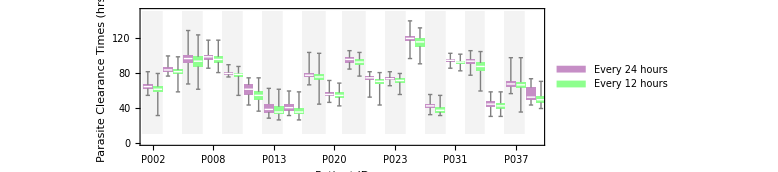

```mathematica
plpct=BoxWhiskerChart[{PLchnDat[[All,ParPosition[#,"PL"]]]&/@ACTpars,PLchnDat[[All,ParPosition[#,"PL"]]]&/@SplitACTpars}ᵀ,AspectRatio->0.3,ImageSize->Large,ChartLabels->{Rotate[#,90Degree]&/@PLid,None},ChartStyle->{Lighter@Lighter@Purple,Lighter@Lighter@Green},ChartLegends->{"Every 24 hours","Every 12 hours"},PlotRange->{{1,40},{0,150}},Prolog->pl,LabelStyle->Directive[Medium,FontFamily->"Times New Roman"],FrameLabel->{{"Parasite Clearance Times (hrs)",None},{"Patient ID",Style["Pailin",Bold,FontSize->14]}}]
```

### Wang Pha

```mathematica
ACTpars="AS7CT."<>ToString@#&/@Range[1,19];
SplitACTpars="SplitCT."<>ToString@#&/@Range[1,19];
```

```mathematica
WPid={"M001","M003","M005","M006","M007","M011","M012","M013","M014","M021","M023","M024","M026","M030","M032","M035","M036","M037","M039"};
```

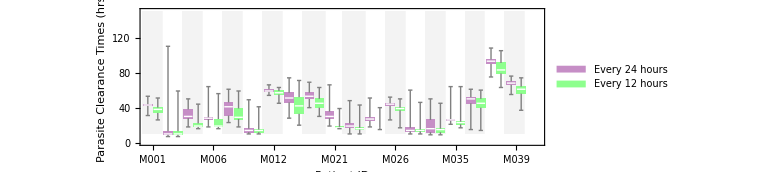

```mathematica
wppct=BoxWhiskerChart[{WPchnDat[[All,ParPosition[#,"WP"]]]&/@ACTpars,WPchnDat[[All,ParPosition[#,"WP"]]]&/@SplitACTpars}ᵀ,AspectRatio->0.3,ImageSize->Large,ChartLabels->{Rotate[#,90Degree]&/@WPid,None},ChartStyle->{Lighter@Lighter@Purple,Lighter@Lighter@Green},ChartLegends->{"Every 24 hours","Every 12 hours"},PlotRange->{{1,40},{0,150}},Prolog->pl,LabelStyle->Directive[Medium,FontFamily->"Times New Roman"],FrameLabel->{{"Parasite Clearance Times (hrs)",None},{"Patient ID",Style["Wang Pha",Bold,FontSize->14]}}]
```

### Wang Pha vs Pailin

```mathematica
Column[{
Labeled[wppct,Style["(A)","Subsubsection",Black],{{Top,Left}}],
Labeled[plpct,Style["(B)","Subsubsection",Black],{{Top,Left}}]},Frame->None]
```

-Graphics-(A)
-Graphics-(B)